```mathematica
Exit
```

```mathematica
T2=({{-1, 1, 1, 1, 1, 1, 0, 0, 0}, {1, -1, 1, 1, 1, 0, 1, 0, 0}, {1, 1, -1, 1, 0, 0, 0, 0, 1}, {1, 1, 1, -1, 1, 0, 0, 1, 0}, {1, 1, 0, 1, -1, -1, -1, -1, -1}, {1, 0, 0, 0, -1, -ⅈ, 1, 1, ⅈ}, {0, 1, 0, 0, -1, 1, -1, -1, 1}, {0, 0, 0, 1, -1, 1, -1, -1, 1}, {0, 0, 1, 0, -1, ⅈ, 1, 1, -ⅈ}});
testFarField=ArrayReshape[IdentityMatrix[9],{3,3,3,3}];
testGrover={{({{-1, 1, 0}, {1, 1, 0}, {0, 0, 0}}),({{1, -1, 0}, {1, 1, 0}, {0, 0, 0}}),({{1, 1, 0}, {-1, 1, 0}, {0, 0, 0}}),({{1, 1, 0}, {1, -1, 0}, {0, 0, 0}})}};
testQFT={{({{0, 0, 0}, {0, 1, 1}, {0, 1, 1}}),({{0, 0, 0}, {0, 1, -ⅈ}, {0, -1, ⅈ}}),({{0, 0, 0}, {0, 1, -1}, {0, 1, -1}}),({{0, 0, 0}, {0, 1, ⅈ}, {0, -1, -ⅈ}})}};
testCNOT={{({{0, 0, 0}, {0, 0, 1}, {0, 0, 0}}),({{0, 0, 0}, {0, 0, 0}, {1, 0, 0}}),({{0, 0, 0}, {0, 0, 0}, {0, 1, 0}}),({{0, 0, 0}, {0, 0, 0}, {0, 0, 1}})}};
```

```mathematica
(* 20um lens*)
p=0.31 2;
size=32p;
λ=0.810;
θx=10Degree;
θy=10Degree;
f=150;
padRatio=5;
```

```mathematica
SetDirectory[NotebookDirectory[]]
Import["./lens-array.m"]
```

/home/stnav/Projects/jensen-lab-mathematica/lens-array

Sample size in um:   {19.84,19.84}

Sample size in pixel:   {32,32}

FAR FIELD LENS

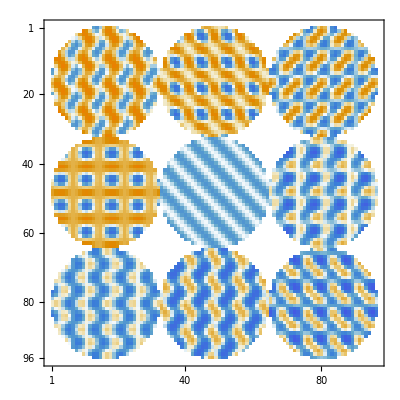

```mathematica
eLocalLens[i_] := 
If[i==0,ConstantArray[0,{ny,nx}],#]&@
Sum[T2[[j]][[i]]* Outer[Times, ⅇ^(ⅈ ky[[j]] (y-y0[[i]])),ⅇ^(ⅈ kx[[j]] (x-x0[[i]]))]*ellipticalMask,{j,9}];

farField[arg_]:=FFT @ArrayPad[eGlobalInput[arg]*meta,{{pady},{padx}}]//Abs[#]^2&;
meta=eGlobalLens[({{1, 2, 3}, {4, 5, 6}, {7, 8, 9}})];
meta//MatrixPlot
```

```mathematica
SetOptions[plot, cropRatio->1];

Echo["FarField"];
plot[farField,testFarField]//Rasterize

Echo["Test Grover"];
plot[farField,testGrover]//Rasterize

Echo["Test QFT"];
plot[farField,testQFT]//Rasterize

Echo["Test CNOT"];
plot[farField,testCNOT]//Rasterize
```

FarField

-Graphics-

Test Grover

-Graphics-

Test QFT

-Graphics-

Test CNOT

-Graphics-

FOCUSING LENS

```mathematica
(*ellipticalMask:=Map[If[#<((lx-p) (ly-p))/4,1,0]&,Outer[Plus,y^2,x^2],{2}];
globalEllipticalMask := KroneckerProduct[({{1, 1, 1}, {1, 1, 1}, {1, 1, 1}}), ellipticalMask];
eGlobalLens[arg_]:= ArrayFlatten[Map[eLocalLens,arg,{2}]];
eGlobalInput[arg_]:=ArrayFlatten[Map[#*ConstantArray[1,{ny,nx}]&,arg,{2}]];
H[A_,z_,{dx_,dy_}] := Module[{nx, ny, kx, ky},
	{nx, ny}=Dimensions[A][[#]]&/@{2,1};
	{kx,ky}=centerRange@@#&/@{{nx, (2π)/(dx nx)},{ny,(2π)/(dy ny)}};
	Exp[ⅈ z Sqrt[k0^2 - Outer[Plus,ky^2,kx^2]]]
]; 
forwardPropagate[A_,z_,{dx_, dy_}]:=iFFT[FFT[A] *H[A,z,{dx, dy}]];*)
```

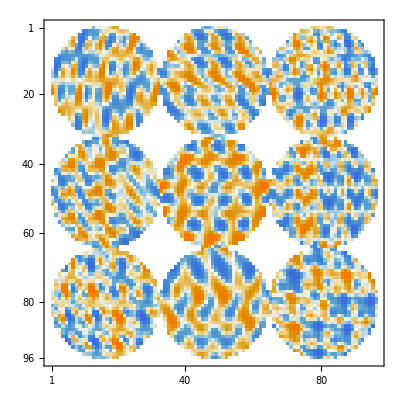

```mathematica
(* Method 1: shift the center of the lens by fx,fy;
	but the lens interference might not be perfect *)
(*eLocalLens[i_] := 
Sum[T2[[j]][[i]]* Exp[-ⅈ*k0*(√(Outer[Plus,(y-y0[[i]]-fy[[j]])^2,(x-x0[[i]]-fx[[j]])^2]+f^2)-f)]
*ellipticalMask,{j,9}];*)

(* Method 2: focus at the center and deflect the beam, but the focusing plane is not parallel with the optical axis. *)
eLocalLens[i_] := 
Sum[T2[[j]][[i]]* Exp[-ⅈ k0√(Outer[Plus,(y-y0[[i]])^2,(x-x0[[i]])^2]+(f^2+fy[[j]]^2+fx[[j]]^2))
+ⅈ Outer[Plus,ky[[j]](y-y0[[i]]),kx[[j]](x-x0[[i]])]]*ellipticalMask,{j,9}];
farField[arg_]:=forwardPropagate[ArrayPad[eGlobalInput[arg]*meta,{{pady}, {padx}}],f, {p, p}]//Abs[#]^2&;
meta=eGlobalLens[({{1, 2, 3}, {4, 5, 6}, {7, 8, 9}})];
meta//MatrixPlot
```

```mathematica
SetOptions[plot, cropRatio->0.5];

Echo["FarField"];
plot[farField,testFarField]//Rasterize

Echo["Test Grover"];
plot[farField,testGrover]//Rasterize

Echo["Test QFT"];
plot[farField,testQFT]//Rasterize

Echo["Test CNOT"];
plot[farField,testCNOT]//Rasterize
```

FarField

-Graphics-

Test Grover

-Graphics-

Test QFT

-Graphics-

Test CNOT

-Graphics-

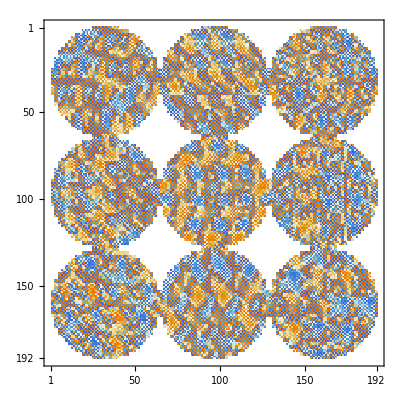

```mathematica
metaPair=convertPair[meta]*KroneckerProduct[globalEllipticalMask,({{1, 1}, {1, 1}})];
farFieldPair[arg_]:=forwardPropagate[
ArrayPad[
KroneckerProduct[eGlobalInput[(arg)],({{1, 1}, {1, 1}})]*metaPair,
2*{{pady},{padx}}],
f,{p/2,p/2}]//Abs[#]^2&;
metaPair//MatrixPlot
```

```mathematica
SetOptions[plot, cropRatio->0.5];

Echo["FarField"];
plot[farFieldPair,testFarField]//Rasterize

Echo["Test Grover"];
plot[farFieldPair,testGrover]//Rasterize

Echo["Test QFT"];
plot[farFieldPair,testQFT]//Rasterize

Echo["Test CNOT"];
plot[farFieldPair,testCNOT]//Rasterize
```

FarField

-Graphics-

Test Grover

-Graphics-

Test QFT

-Graphics-

Test CNOT

-Graphics-

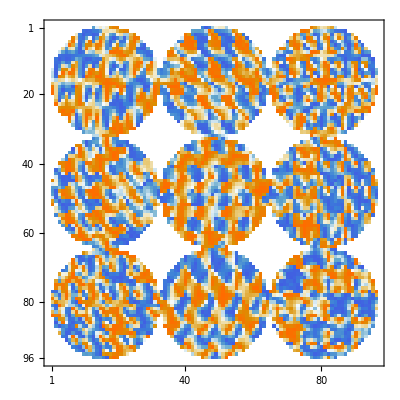

```mathematica
metaArg=convertArg[meta]*globalEllipticalMask;
farFieldArg[arg_]:=forwardPropagate[
ArrayPad[
eGlobalInput[(arg)]*metaArg,
{{pady},{padx}}],
f,{p,p}]//Abs[#]^2&;
metaArg//MatrixPlot
```

```mathematica
SetOptions[plot, cropRatio->0.5];

Echo["FarField"];
plot[farFieldArg,testFarField]//Rasterize

Echo["Test Grover"];
plot[farFieldArg,testGrover]//Rasterize

Echo["Test QFT"];
plot[farFieldArg,testQFT]//Rasterize

Echo["Test CNOT"];
plot[farFieldArg,testCNOT]//Rasterize
```

FarField

-Graphics-

Test Grover

-Graphics-

Test QFT

-Graphics-

Test CNOT

-Graphics-

```mathematica
(* 1mm lens *)
p=0.31 2;
size=1600p;
λ=0.810;
θx=0.2Degree;
θy=0.2Degree;
f=7500;
padRatio=2;
```

```mathematica
SetDirectory[NotebookDirectory[]]
Import["./lens-array.m"]
```

/home/stnav/Projects/jensen-lab-mathematica/lens-array

Sample size in um:   {992.,992.}

Sample size in pixel:   {1600,1600}

```mathematica
eLocalLens[i_] := 
Sum[T2[[j]][[i]]* Exp[-ⅈ k0√(Outer[Plus,(y-y0[[i]])^2,(x-x0[[i]])^2]+(f^2+fy[[j]]^2+fx[[j]]^2))
+ⅈ Outer[Plus,ky[[j]](y-y0[[i]]),kx[[j]](x-x0[[i]])]]*ellipticalMask,{j,9}];
farField[arg_]:=forwardPropagate[ArrayPad[eGlobalInput[arg]*meta,({{pady}, {padx}})],f, {p, p}]//Abs[#]^2&;
meta=eGlobalLens[({{1, 2, 3}, {4, 5, 6}, {7, 8, 9}})];
meta//MatrixPlot//Rasterize//Timing
```

{14.0058,-Graphics-}

```mathematica
SetOptions[plot, cropRatio->0.03];

Echo["FarField"];
plot[farField,{{testFarField[[1]][[1]]}}]//Rasterize

Echo["Test Grover"];
plot[farField,{{testGrover[[1]][[1]]}}]//Rasterize

Echo["Test QFT"];
plot[farField,{{testQFT[[1]][[1]]}}]//Rasterize
```

FarField

-Graphics-

Test Grover

-Graphics-

Test QFT

-Graphics-